## Functions

```mathematica
makeLine[x_, y_, L_, theta_]:={{x, y}, {x+L*Cos[theta], y+L*Sin[theta]}}
```

```mathematica
getSlope[{{xa1_, ya1_}, {xa2_, ya2_}}]:=If[xa2-xa1== 0, "undefined",(ya2-ya1)/(xa2-xa1)]
```

```mathematica
getYintercept[{{xa1_, ya1_}, {xa2_, ya2_}}]:=Module[{m},
m=getSlope[ {{xa1, ya1}, {xa2, ya2}}];
 If[m=="undefined", "undefined", ya1-m*xa1] ]
```

```mathematica
intersectPoint[{{xa1_, ya1_}, {xa2_, ya2_}},  {{xb1_, yb1_}, {xb2_, yb2_}}]:=Module[{mA, mB, bA, bB, yI, xI},
mA=getSlope[{{xa1, ya1}, {xa2, ya2}}];
mB=getSlope[{{xb1, yb1}, {xb2, yb2}}];
bA=getYintercept[{{xa1, ya1}, {xa2, ya2}}];
bB=getYintercept[{{xb1, yb1}, {xb2, yb2}}];
If[mA==mB, {-999, -999},
If[mA=="undefined", If[mB==0, {xa1, yb1}, {xa1, mB*xa1+bB}], 
If[mB=="undefined",If[mA==0, {xb1, ya1},  {xb1, mA*xb1*bA}],
 {(bB-bA)/(mA-mB), mA*(bB-bA)/(mA-mB)+bA}]]]]
```

```mathematica
pointInDomainQ[{{xa1_, ya1_}, {xa2_, ya2_}}, {xb_, yb_}]:=If[((xa1≤ xb ≤ xa2) && (ya1≤ yb ≤ya2)) || 
((xa1>= xb >= xa2) && (ya1<= yb <=ya2)) ||
((xa1>= xb >= xa2) && (ya1>= yb >=ya2)) ||
((xa1<= xb <= xa2) && (ya1>= yb >=ya2))
, True, False]
```

```mathematica
linesIntersectQ[line1_, line2_]:=Module[{point},
point=intersectPoint[line1, line2];
If[{pointInDomainQ[line1, point], pointInDomainQ[line2, point]}=={True, True}, True, False]]
```

```mathematica
makeSquareOffLine[{{xa1_, ya1_}, {xa2_, ya2_}}]:=Module[{L, theta},
L=Sqrt[(xa2-xa1)^2+(ya2-ya1)^2];
theta=ArcTan[(ya2-ya1)/(xa2-xa1)];
{{xa1, ya1}, {xa2, ya2}, {xa2+L*Sin[theta], ya2-L*Cos[theta]}, {xa1+L*Sin[theta], ya1-L*Cos[theta]}}]
```

```mathematica
makeRectangleOffLine[{{xa1_, ya1_}, {xa2_, ya2_}}, L_]:=Module[{ theta},
(* Need to account for time when xa1=xa2 *)
theta=If[xa2==xa1, Pi/2, ArcTan[(ya2-ya1)/(xa2-xa1)]];
{{xa1, ya1}, {xa2, ya2}, {xa2+L*Sin[theta], ya2-L*Cos[theta]}, {xa1+L*Sin[theta], ya1-L*Cos[theta]}}]
```

```mathematica
generateLinesFromPolygon[polygon_]:=Module[{length},
length=Length[polygon];
Append[{polygon[[#]], polygon[[#+1]]}&/@Range[length-1],{ polygon[[length]], polygon[[1]]}]]
```

```mathematica
isPointInPolygon[polygon_, {x_, y_}]:=OddQ[Length[Select[Flatten[linesIntersectQ[#, {{x, y}, {-100, y}}]&/@generateLinesFromPolygon[polygon]],#== True &]]]
```

```mathematica
polygonIntersectQ[polygon1_, polygon2_]:=Module[{lines1, lines2, linesIntersect, cornersInside},
lines1=generateLinesFromPolygon[polygon1];
lines2=generateLinesFromPolygon[polygon2];
linesIntersect=If[MemberQ[Complement[Flatten[Table[Table[{linesIntersectQ[lines2[[j]], lines1[[i]]],linesIntersectQ[lines1[[i]], lines2[[j]]]}, {i, 1, Length[polygon1]}], {j, 1, Length[polygon2]}]]], True], True, False];
cornersInside=MemberQ[Flatten[{isPointInPolygon[polygon1, #]&/@polygon2, isPointInPolygon[polygon2, #]&/@polygon1}], True];
MemberQ[Flatten[{linesIntersect, cornersInside}], True]]
```

```mathematica
polyBoundA={{-1, 0}, {11, 0}, {11, -1}, {-1, -1}};
polyBoundB={{0, -1}, {0, 11}, {-1, 11}, {-1, -1}};
polyBoundC={{-1, 10}, {11, 10}, {11, 11}, {-1, 11}};
polyBoundD={{10, -1}, {10, 11}, {11, 11}, {11, -1}};
boundingPoys={polyBoundA, polyBoundB, polyBoundC, polyBoundD};
```

```mathematica
computePieces[L_, W_, n_]:=Module[{ rectList, newSquare, interSectQ, i},
rectList={};
For[i=1, i<n, i++,
newSquare=makeRectangleOffLine[makeLine[10*Random[],  10*Random[], L,2*Pi*Random[]], W];
interSectQ=Complement[Join[polygonIntersectQ[#, newSquare]&/@boundingPoys, polygonIntersectQ[#, newSquare]&/@rectList]];
rectList=If[interSectQ=={False}, Append[rectList, newSquare], rectList];
If[Mod[i,100]==0, Print[{i,Length[rectList]}]];];
rectList]
```

```mathematica
Round[3*Random[]]/2&/@Range[50]
```

{0,1/2,1/2,1/2,0,0,1,1,1,1,1,1/2,1/2,1/2,0,1/2,1,1/2,1/2,1,0,3/2,3/2,0,3/2,1,1,1,3/2,1,0,0,0,3/2,1/2,1,1,1,1/2,1/2,3/2,0,0,1/2,3/2,1/2,0,1/2,3/2,1}

```mathematica
computePieces3[L_, W_, n_]:=Module[{ rectList, newSquare, interSectQ, i},
rectList={};
For[i=1, i<n, i++,
newSquare=makeRectangleOffLine[makeLine[10*Random[],  10*Random[], L,Pi*Round[3*Random[]]/2], W];
interSectQ=Complement[Join[polygonIntersectQ[#, newSquare]&/@boundingPoys, polygonIntersectQ[#, newSquare]&/@rectList]];
rectList=If[interSectQ=={False}, Append[rectList, newSquare], rectList];
If[Mod[i,100]==0, Print[{i,Length[rectList]}]];];
rectList]
```

```mathematica
computePieces2[L_, W_, n_]:=Module[{ rectList, newSquare, interSectQ, i},
rectList={};
For[i=1, i<n, i++,
newSquare=makeRectangleOffLine[makeLine[10*Random[],  10*Random[], L,0], W];
interSectQ=Complement[Join[polygonIntersectQ[#, newSquare]&/@boundingPoys, polygonIntersectQ[#, newSquare]&/@rectList]];
rectList=If[interSectQ=={False}, Append[rectList, newSquare], rectList];
If[Mod[i,100]==0, Print[{i,Length[rectList]}]];];
rectList]
```

## Work

```mathematica
F[System Size, Aspect Ratio, Number of Runs, Polydispersity, Rotational Freedom] =Value, Variance
```

True

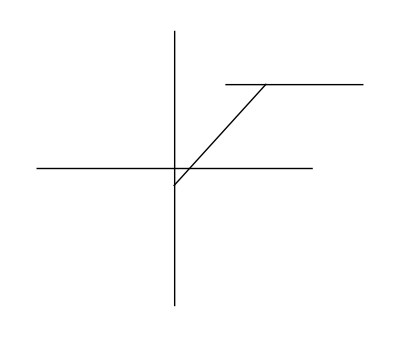

```mathematica
line2=makeLine[Random[],  Random[], 1, 0];
line1=makeLine[Random[],  Random[], 1,2*Pi*Random[]];
Print[linesIntersectQ[line1, line2]];
poin=intersectPoint[line1, line2];
Graphics[{Line[{{-1, 0}, {1, 0}}], Line[{{0, -1}, {0, 1}}], Line[line1],  Line[line2](*, Disk[poin, 0.1]*)}]
```

```mathematica
line1=makeLine[Random[],  Random[], 1,2*Pi*Random[]];
lineList={line1};
For[i=1, i<1000, i++,
newLine=makeLine[Random[],  Random[], 1,2*Pi*Random[]];
interSectQ=Complement[linesIntersectQ[newLine, #]&/@lineList];
lineList=If[interSectQ=={False}, Append[lineList, newLine], lineList];]
```

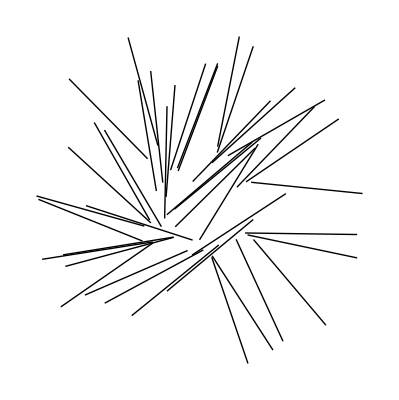

```mathematica
Graphics[{Line[#]&/@lineList}]
```

```mathematica
makeTriangleOffLine[makeLine[10*Random[],  10*Random[], 1,2*Pi*Random[]], 1]
```

{{8.81112,4.80375},{9.649,4.2579},{9.26382,3.36624}}

```mathematica
square1=makeSquareOffLine[makeLine[10*Random[],  10*Random[], 1,2*Pi*Random[]]];
squareList={square1};
For[i=1, i<100, i++,
newSquare=makeSquareOffLine[makeLine[10*Random[],  10*Random[], 1,2*Pi*Random[]]];
interSectQ=Complement[polygonIntersectQ[#, newSquare]&/@squareList];
squareList=If[interSectQ=={False}, Append[squareList, newSquare], squareList];]
```

```mathematica
For[i=1, i<100, i++,
newSquare=makeSquareOffLine[makeLine[10*Random[],  10*Random[], 1,2*Pi*Random[]]];
interSectQ=Complement[polygonIntersectQ[#, newSquare]&/@squareList];
squareList=If[interSectQ=={False}, Append[squareList, newSquare], squareList];]
```

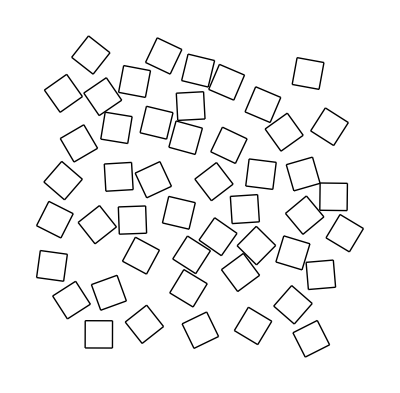

```mathematica
Graphics[{(Line[#]&/@generateLinesFromPolygon[#])&/@squareList}]
```

```mathematica
square1=makeSquareOffLine[makeLine[10*Random[],  10*Random[], 1+2*Random[],2*Pi*Random[]]];
squareList={square1};
For[i=1, i<100, i++,
newSquare=makeSquareOffLine[makeLine[10*Random[],  10*Random[], 1+2*Random[],2*Pi*Random[]]];
interSectQ=Complement[polygonIntersectQ[#, newSquare]&/@squareList];
squareList=If[interSectQ=={False}, Append[squareList, newSquare], squareList];]
```

```mathematica
For[i=1, i<300, i++,
newSquare=makeSquareOffLine[makeLine[10*Random[],  10*Random[], 1+2*Random[],2*Pi*Random[]]];
interSectQ=Complement[polygonIntersectQ[#, newSquare]&/@squareList];
squareList=If[interSectQ=={False}, Append[squareList, newSquare], squareList];]
```

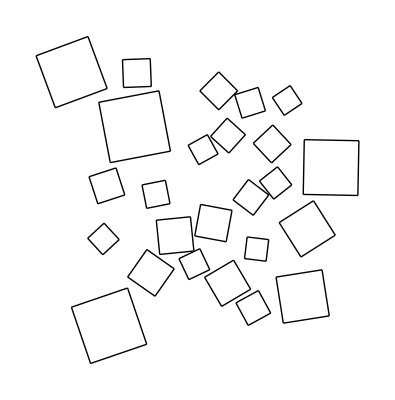

```mathematica
Graphics[{(Line[#]&/@generateLinesFromPolygon[#])&/@squareList}]
```

```mathematica
square1=makeRectangleOffLine[makeLine[10*Random[],  10*Random[], 1,2*Pi*Random[]], 1+Random[]];
squareList={square1};
For[i=1, i<1000, i++,
newSquare=makeRectangleOffLine[makeLine[10*Random[],  10*Random[], 1+2*Random[],2*Pi*Random[]], 1+Random[]];
interSectQ=Complement[polygonIntersectQ[#, newSquare]&/@squareList];
squareList=If[interSectQ=={False}, Append[squareList, newSquare], squareList];]
```

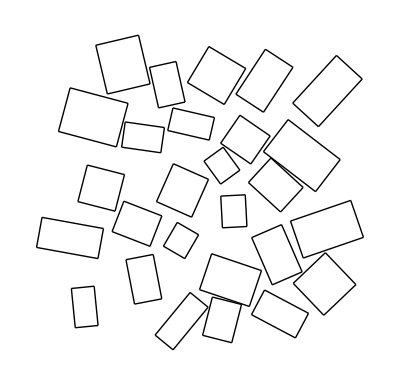

```mathematica
Graphics[{(Line[#]&/@generateLinesFromPolygon[#])&/@squareList}]
```

```mathematica
square1=makeRectangleOffLine[makeLine[10*Random[],  10*Random[], 1,2*Pi*Random[]], 1];
squareList={square1};
For[i=1, i<500, i++,
newSquare=makeRectangleOffLine[makeLine[10*Random[],  10*Random[], 1,2*Pi*Random[]], 1];
interSectQ=Complement[polygonIntersectQ[#, newSquare]&/@squareList];
squareList=If[interSectQ=={False}, Append[squareList, newSquare], squareList];]
```

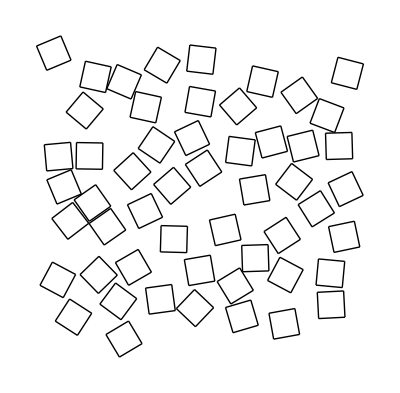

```mathematica
Graphics[{(Line[#]&/@generateLinesFromPolygon[#])&/@squareList}]
```

```mathematica
square1=makeRectangleOffLine[makeLine[10*Random[],  10*Random[], 1/4,2*Pi*Random[]], 4];
rectList={square1};
For[i=1, i<500, i++,
newSquare=makeRectangleOffLine[makeLine[10*Random[],  10*Random[], 1/4,2*Pi*Random[]], 4];
interSectQ=Complement[Join[polygonIntersectQ[#, newSquare]&/@boundingPoys, polygonIntersectQ[#, newSquare]&/@rectList]];
rectList=If[interSectQ=={False}, Append[rectList, newSquare], rectList];]
```

## Current Work

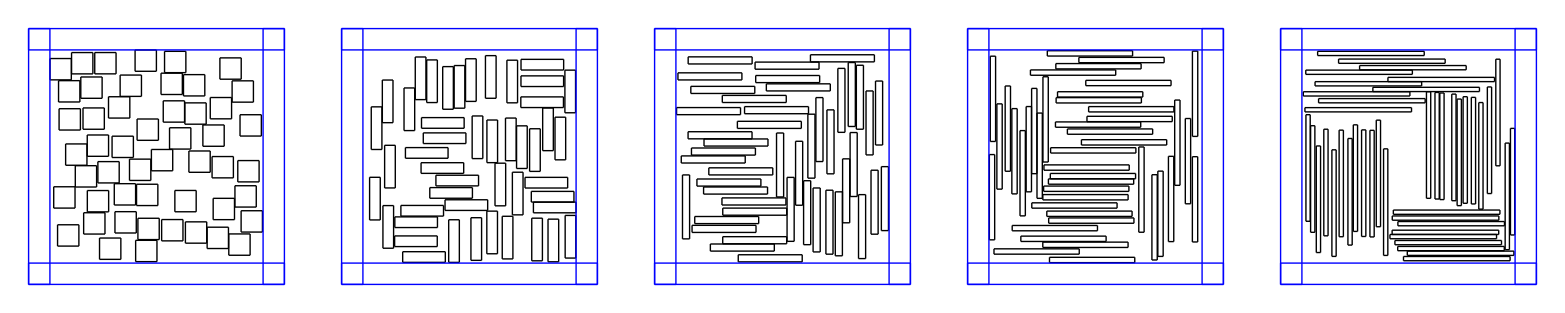

```mathematica
TableForm[{{showResults[qq[[1]]], showResults[qq[[2]]], showResults[qq[[3]]], showResults[qq[[4]]], showResults[qq[[5]]]}}]
```

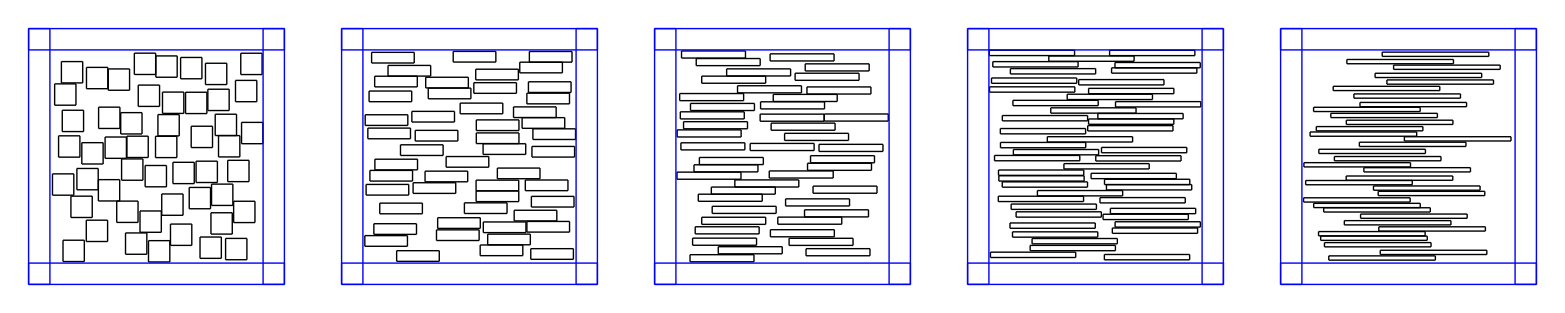

```mathematica
TableForm[{{showResults[qq[[1]]], showResults[qq[[2]]], showResults[qq[[3]]], showResults[qq[[4]]], showResults[qq[[5]]]}}]
```

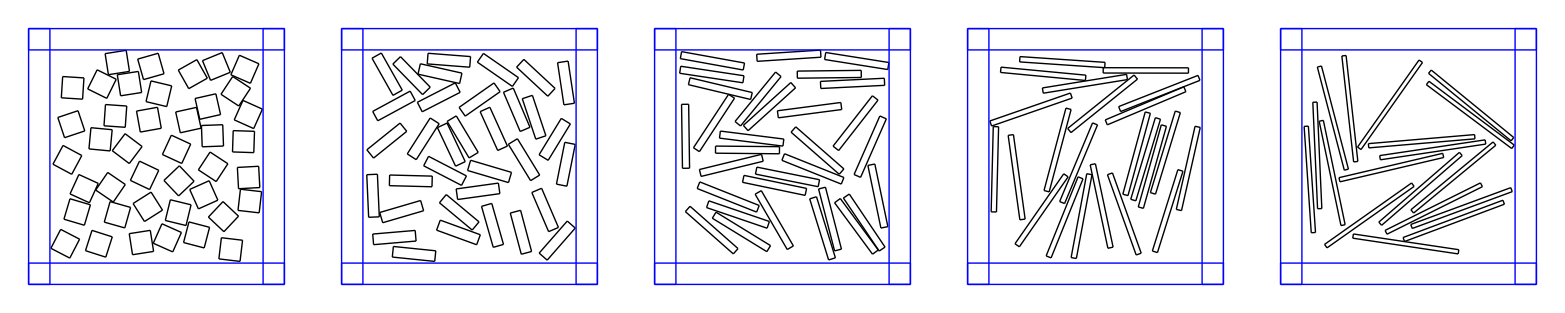

```mathematica
TableForm[{{showResults[qq[[1]]], showResults[qq[[2]]], showResults[qq[[3]]], showResults[qq[[4]]], showResults[qq[[5]]]}}]
```

```mathematica
Length[#]&/@qq
```

{50,47,46,44,43}

```mathematica
zp=computePieces3[3, 1/3, 10]
```

{{{4.17515,5.85234},{4.17515,8.85234},{4.50848,8.85234},{4.50848,5.85234}},{{2.07238,4.81072},{2.07238,7.81072},{2.40572,7.81072},{2.40572,4.81072}},{{5.60812,6.34001},{5.60812,3.34001},{5.94146,3.34001},{5.94146,6.34001}},{{0.075724,0.692668},{3.07572,0.692668},{3.07572,0.359335},{0.075724,0.359335}}}

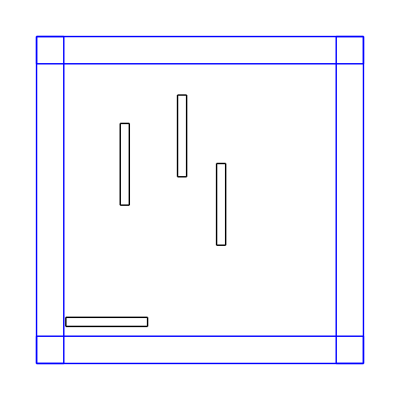

```mathematica
showResults[zp]
```

```mathematica
Length[#]&/@qq
```

{50,47,46,44,43}

```mathematica
qq=computePieces3[#, 1/(#), 2000]&/@Range[5]
```

{100,28}

{200,37}

{300,42}

{400,44}

{500,45}

{600,45}

{700,45}

{800,45}

{900,46}

{1000,46}

{1100,46}

{1200,47}

{1300,48}

{1400,48}

{1500,48}

{1600,50}

{1700,50}

{1800,50}

{1900,50}

{100,26}

{200,31}

{300,34}

{400,38}

{500,38}

{600,41}

{700,43}

{800,43}

{900,44}

{1000,45}

{1100,45}

{1200,45}

{1300,45}

{1400,45}

{1500,46}

{1600,46}

{1700,46}

{1800,46}

{1900,47}

{100,24}

{200,31}

{300,34}

{400,38}

{500,40}

{600,40}

{700,40}

{800,41}

{900,43}

{1000,43}

{1100,45}

{1200,45}

{1300,45}

{1400,46}

{1500,46}

{1600,46}

{1700,46}

{1800,46}

{1900,46}

{100,22}

{200,27}

{300,31}

{400,34}

{500,35}

{600,36}

{700,37}

{800,39}

{900,40}

{1000,41}

{1100,42}

{1200,43}

{1300,43}

{1400,43}

{1500,43}

{1600,43}

{1700,43}

{1800,43}

{1900,44}

{100,17}

{200,24}

{300,26}

{400,31}

{500,32}

{600,34}

{700,37}

{800,37}

{900,37}

{1000,39}

{1100,40}

{1200,40}

{1300,41}

{1400,42}

{1500,42}

{1600,42}

{1700,43}

{1800,43}

{1900,43}

{{{{5.21224,8.90838},{5.21224,7.90838},{6.21224,7.90838},{6.21224,8.90838}},{{7.6584,2.03771},{7.6584,3.03771},{8.6584,3.03771},{8.6584,2.03771}},{{1.55271,7.27819},{1.55271,6.27819},{2.55271,6.27819},{2.55271,7.27819}},{{4.76067,5.32939},{4.76067,4.32939},{5.76067,4.32939},{5.76067,5.32939}},{{2.10315,8.8765},{2.10315,9.8765},{3.10315,9.8765},{3.10315,8.8765}},{{8.96918,2.45566},{9.96918,2.45566},{9.96918,1.45566},{8.96918,1.45566}},{{3.05129,1.41188},{3.05129,2.41188},{4.05129,2.41188},{4.05129,1.41188}},{{7.60672,3.9979},{7.60672,4.9979},{8.60672,4.9979},{8.60672,3.9979}},{{1.44899,8.73023},{1.44899,7.73023},{2.44899,7.73023},{2.44899,8.73023}},{{6.35585,0.934567},{6.35585,1.93457},{7.35585,1.93457},{7.35585,0.934567}},{{2.91579,4.9532},{2.91579,5.9532},{3.91579,5.9532},{3.91579,4.9532}},{{6.86121,3.40725},{5.86121,3.40725},{5.86121,2.40725},{6.86121,2.40725}},{{4.08995,6.75899},{4.08995,5.75899},{5.08995,5.75899},{5.08995,6.75899}},{{8.54641,8.54937},{9.54641,8.54937},{9.54641,7.54937},{8.54641,7.54937}},{{6.31632,7.61184},{5.31632,7.61184},{5.31632,6.61184},{6.31632,6.61184}},{{3.74861,7.80296},{2.74861,7.80296},{2.74861,6.80296},{3.74861,6.80296}},{{7.33023,7.51567},{6.33023,7.51567},{6.33023,6.51567},{7.33023,6.51567}},{{8.17544,6.47973},{7.17544,6.47973},{7.17544,5.47973},{8.17544,5.47973}},{{8.97387,9.62606},{7.97387,9.62606},{7.97387,8.62606},{8.97387,8.62606}},{{1.58275,1.36204},{1.58275,2.36204},{2.58275,2.36204},{2.58275,1.36204}},{{8.52208,7.76692},{7.52208,7.76692},{7.52208,6.76692},{8.52208,6.76692}},{{5.24122,2.04235},{5.24122,1.04235},{6.24122,1.04235},{6.24122,2.04235}},{{1.19051,4.56875},{2.19051,4.56875},{2.19051,3.56875},{1.19051,3.56875}},{{2.32773,0.175208},{2.32773,1.17521},{3.32773,1.17521},{3.32773,0.175208}},{{0.430329,7.24149},{0.430329,6.24149},{1.43033,6.24149},{1.43033,7.24149}},{{0.358993,0.797291},{0.358993,1.79729},{1.35899,1.79729},{1.35899,0.797291}},{{3.29443,7.82007},{3.29443,8.82007},{4.29443,8.82007},{4.29443,7.82007}},{{8.91812,6.95939},{8.91812,5.95939},{9.91812,5.95939},{9.91812,6.95939}},{{5.06332,3.69871},{4.06332,3.69871},{4.06332,2.69871},{5.06332,2.69871}},{{6.26581,8.8407},{7.26581,8.8407},{7.26581,7.8407},{6.26581,7.8407}},{{6.61144,6.34839},{5.61144,6.34839},{5.61144,5.34839},{6.61144,5.34839}},{{2.2502,3.76027},{2.2502,4.76027},{3.2502,4.76027},{3.2502,3.76027}},{{6.51937,4.25888},{6.51937,5.25888},{7.51937,5.25888},{7.51937,4.25888}},{{0.737526,5.58941},{1.73753,5.58941},{1.73753,4.58941},{0.737526,4.58941}},{{4.9955,9.9974},{3.9955,9.9974},{3.9955,8.9974},{4.9955,8.9974}},{{8.81266,4.80894},{8.81266,3.80894},{9.81266,3.80894},{9.81266,4.80894}},{{1.40521,8.55779},{0.405212,8.55779},{0.405212,7.55779},{1.40521,7.55779}},{{3.0193,2.72492},{3.0193,3.72492},{4.0193,3.72492},{4.0193,2.72492}},{{8.39106,1.36777},{8.39106,0.367769},{9.39106,0.367769},{9.39106,1.36777}},{{0.178406,2.58005},{0.178406,3.58005},{1.17841,3.58005},{1.17841,2.58005}},{{1.01552,9.87546},{1.01552,8.87546},{2.01552,8.87546},{2.01552,9.87546}},{{4.12788,2.10257},{4.12788,1.10257},{5.12788,1.10257},{5.12788,2.10257}},{{8.67947,2.6283},{8.67947,3.6283},{9.67947,3.6283},{9.67947,2.6283}},{{5.37735,9.9334},{5.37735,8.9334},{6.37735,8.9334},{6.37735,9.9334}},{{3.73363,4.87651},{3.73363,3.87651},{4.73363,3.87651},{4.73363,4.87651}},{{1.75511,3.40316},{1.75511,2.40316},{2.75511,2.40316},{2.75511,3.40316}},{{1.00447,9.59522},{0.00446968,9.59522},{0.00446968,8.59522},{1.00447,8.59522}},{{7.37539,1.68348},{7.37539,0.683483},{8.37539,0.683483},{8.37539,1.68348}},{{1.75141,6.00919},{2.75141,6.00919},{2.75141,5.00919},{1.75141,5.00919}},{{4.02166,1.06827},{4.02166,0.0682696},{5.02166,0.0682696},{5.02166,1.06827}}},{{{6.75448,9.51775},{6.75448,7.51775},{7.25448,7.51775},{7.25448,9.51775}},{{5.81241,0.437274},{5.81241,2.43727},{6.31241,2.43727},{6.31241,0.437274}},{{0.313614,4.02424},{0.313614,2.02424},{0.813614,2.02424},{0.813614,4.02424}},{{9.40714,7.79628},{7.40714,7.79628},{7.40714,7.29628},{9.40714,7.29628}},{{3.99426,5.41784},{1.99426,5.41784},{1.99426,4.91784},{3.99426,4.91784}},{{1.92888,8.21551},{1.92888,6.21551},{2.42888,6.21551},{2.42888,8.21551}},{{6.68853,4.80331},{6.68853,6.80331},{7.18853,6.80331},{7.18853,4.80331}},{{8.68337,0.0612711},{8.68337,2.06127},{9.18337,2.06127},{9.18337,0.0612711}},{{0.911029,8.58643},{0.911029,6.58643},{1.41103,6.58643},{1.41103,8.58643}},{{4.8317,6.10772},{2.8317,6.10772},{2.8317,5.60772},{4.8317,5.60772}},{{1.49684,2.16741},{3.49684,2.16741},{3.49684,1.66741},{1.49684,1.66741}},{{3.42452,4.12129},{5.42452,4.12129},{5.42452,3.62129},{3.42452,3.62129}},{{7.89934,3.36325},{9.89934,3.36325},{9.89934,2.86325},{7.89934,2.86325}},{{4.02365,0.0328592},{4.02365,2.03286},{4.52365,2.03286},{4.52365,0.0328592}},{{7.01133,4.26262},{7.01133,2.26262},{7.51133,2.26262},{7.51133,4.26262}},{{9.01116,4.84392},{9.01116,6.84392},{9.51116,6.84392},{9.51116,4.84392}},{{5.12447,4.90155},{5.12447,6.90155},{5.62447,6.90155},{5.62447,4.90155}},{{7.81883,6.30151},{7.81883,4.30151},{8.31883,4.30151},{8.31883,6.30151}},{{4.81405,7.58455},{4.81405,9.58455},{5.31405,9.58455},{5.31405,7.58455}},{{5.85243,2.97035},{3.85243,2.97035},{3.85243,2.47035},{5.85243,2.47035}},{{7.92006,0.10687},{7.92006,2.10687},{8.42006,2.10687},{8.42006,0.10687}},{{0.391372,7.32929},{0.391372,5.32929},{0.891372,5.32929},{0.891372,7.32929}},{{1.01876,3.52519},{1.01876,5.52519},{1.51876,5.52519},{1.51876,3.52519}},{{5.74791,9.73133},{5.74791,7.73133},{6.24791,7.73133},{6.24791,9.73133}},{{3.48773,1.27432},{1.48773,1.27432},{1.48773,0.774318},{3.48773,0.774318}},{{5.1372,3.54172},{3.1372,3.54172},{3.1372,3.04172},{5.1372,3.04172}},{{3.74263,7.21643},{3.74263,9.21643},{4.24263,9.21643},{4.24263,7.21643}},{{1.78139,2.70446},{3.78139,2.70446},{3.78139,2.20446},{1.78139,2.20446}},{{9.41664,9.55686},{7.41664,9.55686},{7.41664,9.05686},{9.41664,9.05686}},{{9.48735,0.235921},{9.48735,2.23592},{9.98735,2.23592},{9.98735,0.235921}},{{7.60447,4.0215},{9.60447,4.0215},{9.60447,3.5215},{7.60447,3.5215}},{{2.99195,7.53033},{2.99195,9.53033},{3.49195,9.53033},{3.49195,7.53033}},{{7.20776,4.43789},{7.20776,6.43789},{7.70776,6.43789},{7.70776,4.43789}},{{6.53587,0.196044},{6.53587,2.19604},{7.03587,2.19604},{7.03587,0.196044}},{{2.72795,4.70896},{4.72795,4.70896},{4.72795,4.20896},{2.72795,4.20896}},{{5.81681,6.71156},{5.81681,4.71156},{6.31681,4.71156},{6.31681,6.71156}},{{8.43234,5.27416},{8.43234,7.27416},{8.93234,7.27416},{8.93234,5.27416}},{{6.19645,2.68639},{6.19645,4.68639},{6.69645,4.68639},{6.69645,2.68639}},{{4.74869,6.82455},{2.74869,6.82455},{2.74869,6.32455},{4.74869,6.32455}},{{1.8655,0.534246},{3.8655,0.534246},{3.8655,0.0342458},{1.8655,0.0342458}},{{2.45585,7.66806},{2.45585,9.66806},{2.95585,9.66806},{2.95585,7.66806}},{{4.28039,9.26636},{4.28039,7.26636},{4.78039,7.26636},{4.78039,9.26636}},{{0.939225,2.69746},{0.939225,0.697462},{1.43922,0.697462},{1.43922,2.69746}},{{9.41397,8.78209},{7.41397,8.78209},{7.41397,8.28209},{9.41397,8.28209}},{{9.47499,7.05112},{9.47499,9.05112},{9.97499,9.05112},{9.97499,7.05112}},{{5.06702,0.128712},{5.06702,2.12871},{5.56702,2.12871},{5.56702,0.128712}},{{9.99807,2.8584},{7.99807,2.8584},{7.99807,2.3584},{9.99807,2.3584}}},{{{7.24218,8.40874},{4.24218,8.40874},{4.24218,8.07541},{7.24218,8.07541}},{{6.7133,9.42827},{3.7133,9.42827},{3.7133,9.09493},{6.7133,9.09493}},{{3.03075,7.29528},{0.0307456,7.29528},{0.0307456,6.96195},{3.03075,6.96195}},{{9.36351,5.53963},{9.36351,8.53963},{9.69684,8.53963},{9.69684,5.53963}},{{0.75757,1.77142},{3.75757,1.77142},{3.75757,1.43809},{0.75757,1.43809}},{{8.91811,5.07449},{8.91811,8.07449},{9.25144,8.07449},{9.25144,5.07449}},{{7.81886,1.89012},{7.81886,4.89012},{8.15219,4.89012},{8.15219,1.89012}},{{6.43532,0.523582},{6.43532,3.52358},{6.76866,3.52358},{6.76866,0.523582}},{{4.61616,0.895698},{1.61616,0.895698},{1.61616,0.562365},{4.61616,0.562365}},{{0.570656,6.16221},{3.57066,6.16221},{3.57066,5.82888},{0.570656,5.82888}},{{6.74294,8.79924},{3.74294,8.79924},{3.74294,8.4659},{6.74294,8.4659}},{{6.18951,3.98446},{6.18951,6.98446},{6.52284,6.98446},{6.52284,3.98446}},{{8.08307,6.40832},{8.08307,9.40832},{8.4164,9.40832},{8.4164,6.40832}},{{7.08432,7.18737},{7.08432,4.18737},{7.41765,4.18737},{7.41765,7.18737}},{{3.98597,3.94484},{0.985973,3.94484},{0.985973,3.6115},{3.98597,3.6115}},{{5.16004,3.05796},{2.16004,3.05796},{2.16004,2.72463},{5.16004,2.72463}},{{8.56604,3.21129},{8.56604,0.211295},{8.89937,0.211295},{8.89937,3.21129}},{{5.98941,0.864028},{5.98941,3.86403},{6.32274,3.86403},{6.32274,0.864028}},{{0.308748,1.1358},{0.308748,4.1358},{0.642081,4.1358},{0.642081,1.1358}},{{5.17593,7.86602},{2.17593,7.86602},{2.17593,7.53269},{5.17593,7.53269}},{{5.2139,4.0203},{5.2139,1.0203},{5.54724,1.0203},{5.54724,4.0203}},{{5.9245,0.39117},{2.9245,0.39117},{2.9245,0.0578371},{5.9245,0.0578371}},{{0.883233,2.18528},{3.88323,2.18528},{3.88323,1.85195},{0.883233,1.85195}},{{2.88347,6.65076},{5.88347,6.65076},{5.88347,6.31743},{2.88347,6.31743}},{{4.29817,3.57007},{1.29817,3.57007},{1.29817,3.23674},{4.29817,3.23674}},{{8.17099,3.12409},{8.17099,6.12409},{8.50432,6.12409},{8.50432,3.12409}},{{0.729626,5.39917},{3.72963,5.39917},{3.72963,5.06584},{0.729626,5.06584}},{{3.5751,9.67416},{0.575096,9.67416},{0.575096,9.34083},{3.5751,9.34083}},{{7.47637,0.34214},{7.47637,3.34214},{7.8097,3.34214},{7.8097,0.34214}},{{4.71992,3.10239},{4.71992,6.10239},{5.05326,6.10239},{5.05326,3.10239}},{{5.61326,5.71412},{5.61326,2.71412},{5.94659,2.71412},{5.94659,5.71412}},{{3.21995,7.33993},{6.21995,7.33993},{6.21995,7.00659},{3.21995,7.00659}},{{2.196,1.23886},{5.196,1.23886},{5.196,0.905523},{2.196,0.905523}},{{9.31088,9.77253},{6.31088,9.77253},{6.31088,9.4392},{9.31088,9.4392}},{{4.31833,5.82287},{1.31833,5.82287},{1.31833,5.48953},{4.31833,5.48953}},{{8.46376,6.27982},{8.46376,9.27982},{8.7971,9.27982},{8.7971,6.27982}},{{9.15243,1.35624},{9.15243,4.35624},{9.48576,4.35624},{9.48576,1.35624}},{{3.69982,8.29017},{0.699816,8.29017},{0.699816,7.95684},{3.69982,7.95684}},{{7.03612,0.418475},{7.03612,3.41847},{7.36946,3.41847},{7.36946,0.418475}},{{7.59655,6.13326},{7.59655,9.13326},{7.92989,9.13326},{7.92989,6.13326}},{{4.54355,4.46899},{1.54355,4.46899},{1.54355,4.13566},{4.54355,4.13566}},{{0.0956142,8.92459},{3.09561,8.92459},{3.09561,8.59125},{0.0956142,8.59125}},{{2.1978,2.57925},{5.1978,2.57925},{5.1978,2.24591},{2.1978,2.24591}},{{6.56644,7.76348},{6.56644,4.76348},{6.89978,4.76348},{6.89978,7.76348}},{{3.25127,5.02787},{0.251265,5.02787},{0.251265,4.69454},{3.25127,4.69454}},{{9.63748,4.52439},{9.63748,1.52439},{9.97082,1.52439},{9.97082,4.52439}}},{{{7.03049,5.44734},{7.03049,1.44734},{7.28049,1.44734},{7.28049,5.44734}},{{6.56668,3.61332},{2.56668,3.61332},{2.56668,3.36332},{6.56668,3.36332}},{{7.64627,0.14576},{7.64627,4.14576},{7.89627,4.14576},{7.89627,0.14576}},{{8.54409,8.57261},{4.54409,8.57261},{4.54409,8.32261},{8.54409,8.32261}},{{4.59994,6.88545},{8.59994,6.88545},{8.59994,6.63545},{4.59994,6.63545}},{{4.67732,7.34073},{8.67732,7.34073},{8.67732,7.09073},{4.67732,7.09073}},{{0.762798,4.308},{0.762798,8.308},{1.0128,8.308},{1.0128,4.308}},{{9.54387,0.990957},{9.54387,4.99096},{9.79387,4.99096},{9.79387,0.990957}},{{6.52954,3.2137},{2.52954,3.2137},{2.52954,2.9637},{6.52954,2.9637}},{{8.33995,5.78854},{4.33995,5.78854},{4.33995,5.53854},{8.33995,5.53854}},{{2.25557,7.03746},{2.25557,3.03746},{2.50557,3.03746},{2.50557,7.03746}},{{5.49777,1.26462},{1.49777,1.26462},{1.49777,1.01462},{5.49777,1.01462}},{{8.71443,7.64781},{8.71443,3.64781},{8.96443,3.64781},{8.96443,7.64781}},{{7.13942,9.35932},{3.13942,9.35932},{3.13942,9.10932},{7.13942,9.10932}},{{1.07601,3.24648},{1.07601,7.24648},{1.32601,7.24648},{1.32601,3.24648}},{{6.89383,5.41235},{2.89383,5.41235},{2.89383,5.16235},{6.89383,5.16235}},{{2.53467,8.74098},{2.53467,4.74098},{2.78467,4.74098},{2.78467,8.74098}},{{9.5464,5.94285},{9.5464,9.94285},{9.7964,9.94285},{9.7964,5.94285}},{{1.74705,3.34287},{1.74705,7.34287},{1.99705,7.34287},{1.99705,3.34287}},{{9.2129,2.78161},{9.2129,6.78161},{9.4629,6.78161},{9.4629,2.78161}},{{6.88001,4.20491},{2.88001,4.20491},{2.88001,3.95491},{6.88001,3.95491}},{{2.8416,0.271173},{6.8416,0.271173},{6.8416,0.0211725},{2.8416,0.0211725}},{{5.948,9.06128},{1.948,9.06128},{1.948,8.81128},{5.948,8.81128}},{{4.23798,0.668824},{0.237978,0.668824},{0.237978,0.418824},{4.23798,0.418824}},{{1.45888,6.21487},{1.45888,2.21487},{1.70888,2.21487},{1.70888,6.21487}},{{7.21898,8.03827},{3.21898,8.03827},{3.21898,7.78827},{7.21898,7.78827}},{{7.92415,4.31362},{7.92415,0.313615},{8.17415,0.313615},{8.17415,4.31362}},{{2.52777,0.983557},{6.52777,0.983557},{6.52777,0.733557},{2.52777,0.733557}},{{2.71592,2.43953},{6.71592,2.43953},{6.71592,2.18953},{2.71592,2.18953}},{{1.09237,1.76464},{5.09237,1.76464},{5.09237,1.51464},{1.09237,1.51464}},{{8.4213,1.00793},{8.4213,5.00793},{8.6713,5.00793},{8.6713,1.00793}},{{7.6811,6.29353},{3.6811,6.29353},{3.6811,6.04353},{7.6811,6.04353}},{{0.373675,7.46912},{0.373675,3.46912},{0.623675,3.46912},{0.623675,7.46912}},{{4.21985,9.65037},{8.21985,9.65037},{8.21985,9.40037},{4.21985,9.40037}},{{7.15281,7.76143},{3.15281,7.76143},{3.15281,7.51143},{7.15281,7.51143}},{{6.8031,2.11881},{2.8031,2.11881},{2.8031,1.86881},{6.8031,1.86881}},{{0.0637641,9.70563},{0.0637641,5.70563},{0.313764,5.70563},{0.313764,9.70563}},{{7.12153,6.62214},{3.12153,6.62214},{3.12153,6.37214},{7.12153,6.37214}},{{6.79094,3.95015},{2.79094,3.95015},{2.79094,3.70015},{6.79094,3.70015}},{{2.00317,8.19449},{2.00317,4.19449},{2.25317,4.19449},{2.25317,8.19449}},{{6.01196,2.827},{2.01196,2.827},{2.01196,2.577},{6.01196,2.577}},{{6.73957,9.96222},{2.73957,9.96222},{2.73957,9.71222},{6.73957,9.71222}},{{2.58197,4.60656},{6.58197,4.60656},{6.58197,4.35656},{2.58197,4.35656}},{{0.0205115,1.09057},{0.0205115,5.09057},{0.270511,5.09057},{0.270511,1.09057}}},{{{9.28871,2.48813},{4.28871,2.48813},{4.28871,2.28813},{9.28871,2.28813}},{{9.5341,0.629252},{9.5341,5.62925},{9.7341,5.62925},{9.7341,0.629252}},{{5.61693,8.51113},{0.616931,8.51113},{0.616931,8.31113},{5.61693,8.31113}},{{5.78184,7.71671},{0.781839,7.71671},{0.781839,7.51671},{5.78184,7.51671}},{{3.83019,5.35962},{3.83019,0.359623},{4.03019,0.359623},{4.03019,5.35962}},{{9.12998,1.34205},{4.12998,1.34205},{4.12998,1.14205},{9.12998,1.14205}},{{2.41092,1.48565},{2.41092,6.48565},{2.61092,6.48565},{2.61092,1.48565}},{{0.674499,0.49485},{0.674499,5.49485},{0.874499,5.49485},{0.874499,0.49485}},{{0.141765,7.29242},{5.14177,7.29242},{5.14177,7.09242},{0.141765,7.09242}},{{9.09547,4.56401},{9.09547,9.56401},{9.29547,9.56401},{9.29547,4.56401}},{{9.03517,8.71197},{4.03517,8.71197},{4.03517,8.51197},{9.03517,8.51197}},{{5.84221,3.03845},{5.84221,8.03845},{6.04221,8.03845},{6.04221,3.03845}},{{1.40655,0.313806},{1.40655,5.31381},{1.60655,5.31381},{1.60655,0.313806}},{{7.28061,2.69458},{7.28061,7.69458},{7.48061,7.69458},{7.48061,2.69458}},{{7.70608,9.26674},{2.70608,9.26674},{2.70608,9.06674},{7.70608,9.06674}},{{1.74552,1.2363},{1.74552,6.2363},{1.94552,6.2363},{1.94552,1.2363}},{{2.15827,5.84501},{2.15827,0.845007},{2.35827,0.845007},{2.35827,5.84501}},{{0.737442,9.93493},{5.73744,9.93493},{5.73744,9.73493},{0.737442,9.73493}},{{9.76521,0.310033},{4.76521,0.310033},{4.76521,0.110033},{9.76521,0.110033}},{{6.46918,7.97903},{6.46918,2.97903},{6.66918,2.97903},{6.66918,7.97903}},{{0.18897,1.9616},{0.18897,6.9616},{0.38897,6.9616},{0.38897,1.9616}},{{2.79908,1.24862},{2.79908,6.24862},{2.99908,6.24862},{2.99908,1.24862}},{{9.78271,6.31911},{9.78271,1.31911},{9.98271,1.31911},{9.98271,6.31911}},{{7.94706,2.77395},{7.94706,7.77395},{8.14706,7.77395},{8.14706,2.77395}},{{6.71983,9.57081},{1.71983,9.57081},{1.71983,9.37081},{6.71983,9.37081}},{{1.02684,6.27956},{1.02684,1.27956},{1.22684,1.27956},{1.22684,6.27956}},{{3.48795,6.70538},{3.48795,1.70538},{3.68795,1.70538},{3.68795,6.70538}},{{7.03016,2.92655},{7.03016,7.92655},{7.23016,7.92655},{7.23016,2.92655}},{{0.181383,9.05231},{5.18138,9.05231},{5.18138,8.85231},{0.181383,8.85231}},{{3.32864,8.24595},{8.32864,8.24595},{8.32864,8.04595},{3.32864,8.04595}},{{9.94349,0.561205},{4.94349,0.561205},{4.94349,0.361205},{9.94349,0.361205}},{{9.36255,1.06059},{4.36255,1.06059},{4.36255,0.860592},{9.36255,0.860592}},{{9.50205,1.94954},{4.50205,1.94954},{4.50205,1.74954},{9.50205,1.74954}},{{8.69847,3.26231},{8.69847,8.26231},{8.89847,8.26231},{8.89847,3.26231}},{{6.24167,8.00555},{6.24167,3.00555},{6.44167,3.00555},{6.44167,8.00555}},{{0.408002,1.44403},{0.408002,6.44403},{0.608002,6.44403},{0.608002,1.44403}},{{3.19038,1.22724},{3.19038,6.22724},{3.39038,6.22724},{3.39038,1.22724}},{{8.29652,2.53058},{8.29652,7.53058},{8.49652,7.53058},{8.49652,2.53058}},{{5.06504,8.03725},{0.0650357,8.03725},{0.0650357,7.83725},{5.06504,7.83725}},{{4.23802,2.21145},{9.23802,2.21145},{9.23802,2.01145},{4.23802,2.01145}},{{9.49305,0.781441},{4.49305,0.781441},{4.49305,0.581441},{9.49305,0.581441}},{{7.56107,2.80519},{7.56107,7.80519},{7.76107,7.80519},{7.76107,2.80519}},{{9.23196,1.54325},{4.23196,1.54325},{4.23196,1.34325},{9.23196,1.34325}}}}

```mathematica
Length[qq[[5]]]
```

34

```mathematica
az=%;
```

```mathematica
Mod[110, 100]
```

10

```mathematica
ss=Table[{1/(i*Sqrt[2]), i/Sqrt[2],Length[computePieces[1/(i*Sqrt[2]), i/Sqrt[2], 500]]}, {i, 1,5}]
```

{{1/(√2),1/(√2),61},{1/(2 √2),√2,58},{1/(3 √2),3/(√2),44},{1/(4 √2),2 √2,32},{1/(5 √2),5/(√2),24}}

```mathematica
Table[{i*100,Length[computePieces[1/(i*Sqrt[2]), i/Sqrt[2], 500]]}, {i, 1,5}]
```

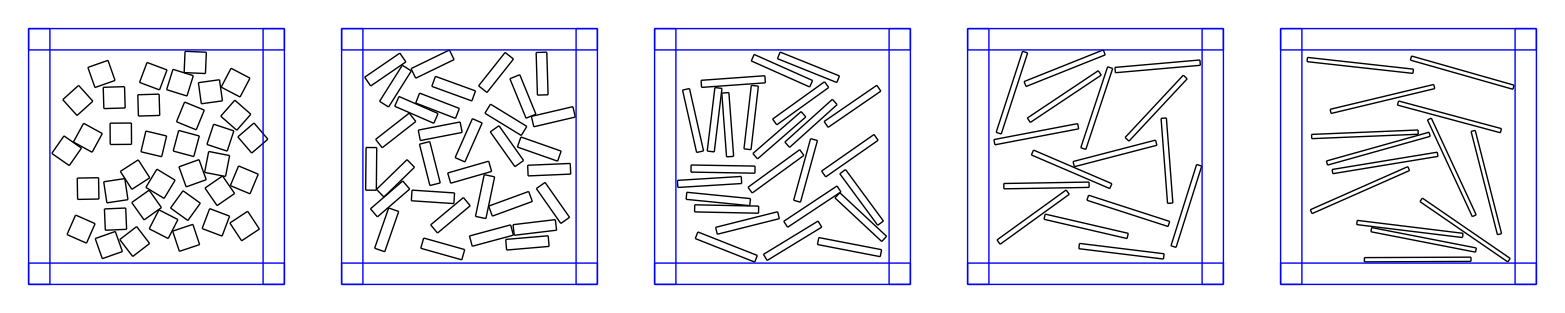

```mathematica
TableForm[{{Graphics[{ Black,(Line[#]&/@generateLinesFromPolygon[#])&/@oneB1,Blue,(Line[#]&/@generateLinesFromPolygon[#])&/@boundingPoys}],
Graphics[{ Black,(Line[#]&/@generateLinesFromPolygon[#])&/@P5B2,Blue,(Line[#]&/@generateLinesFromPolygon[#])&/@boundingPoys}],
Graphics[{ Black,(Line[#]&/@generateLinesFromPolygon[#])&/@P3B3,Blue,(Line[#]&/@generateLinesFromPolygon[#])&/@boundingPoys}],
Graphics[{ Black,(Line[#]&/@generateLinesFromPolygon[#])&/@P25B4,Blue,(Line[#]&/@generateLinesFromPolygon[#])&/@boundingPoys}],
Graphics[{ Black,(Line[#]&/@generateLinesFromPolygon[#])&/@P2B5,Blue,(Line[#]&/@generateLinesFromPolygon[#])&/@boundingPoys}]}}]
```

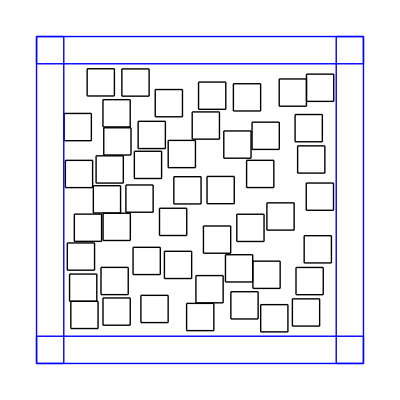

```mathematica
Graphics[{ Black,(Line[#]&/@generateLinesFromPolygon[#])&/@qq,Blue,(Line[#]&/@generateLinesFromPolygon[#])&/@boundingPoys}]
```

```mathematica
N[100/Pi]
```

31.831

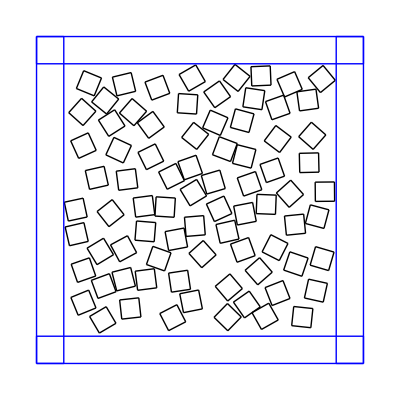

```mathematica
Graphics[{ Black,(Line[#]&/@generateLinesFromPolygon[#])&/@qq,Blue,(Line[#]&/@generateLinesFromPolygon[#])&/@boundingPoys}]
```

## Triangles

```mathematica
makeTriangleOffLine[{{xa1_, ya1_}, {xa2_, ya2_}}, L_]:=Module[{ theta},
(* Need to account for time when xa1=xa2 *)
theta=If[xa2==xa1, Pi/2, ArcTan[(ya2-ya1)/(xa2-xa1)]];
{{xa1, ya1}, {xa2, ya2}, {xa1+L*Cos[theta+Pi/3], ya1+L*Sin[theta+Pi/3]}}]
```

```mathematica
makeTriangle[x_, y_, L_, H_, theta_]:=(RotationMatrix[theta].#+{x,y})&/@{{0, 0}, {L, 0}, {L/2, H}}
```

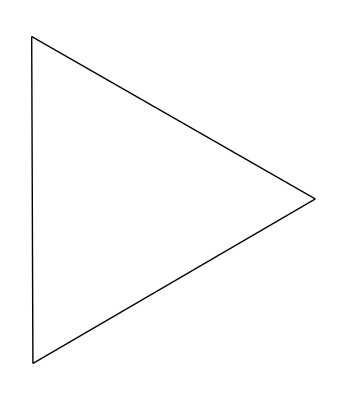

```mathematica
Graphics[{(Line[#]&/@generateLinesFromPolygon[makeTriangleOffLine[makeLine[0,  0, 1,0.5*Pi*Random[]], 1]])}]
```

```mathematica
tri1=makeTriangle[10*Random[], 10*Random[], 4/Sqrt[3], Sqrt[3]/2, 2*Pi*Random[]];
triList={};
For[i=1, i<=1000, i++,
newTri=makeTriangle[10*Random[], 10*Random[], 4/Sqrt[3], Sqrt[3]/2, 2*Pi*Random[]];
interSectQ=Complement[Join[polygonIntersectQ[#, newTri]&/@boundingPoys, polygonIntersectQ[#, newTri]&/@triList]];
triList=If[interSectQ=={False}, Append[triList, newTri], triList];
If[Mod[i,100]==0, Print[{i, Length[triList]}]];]
```

{100,22}

{200,27}

{300,27}

{400,29}

{500,30}

{600,32}

{700,32}

{800,32}

{900,32}

{1000,32}

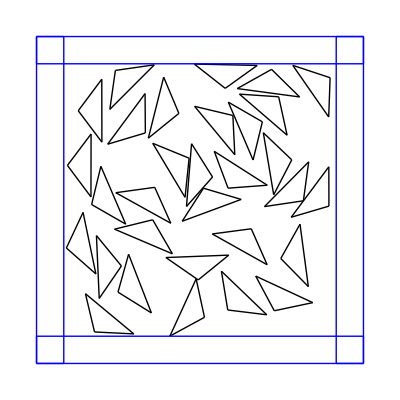

```mathematica
Graphics[{ Black,(Line[#]&/@generateLinesFromPolygon[#])&/@Rest[triList],Blue,(Line[#]&/@generateLinesFromPolygon[#])&/@boundingPoys}]
```

```mathematica
tri1=makeTriangle[10*Random[], 10*Random[], 2/Sqrt[3], Sqrt[3], 2*Pi*Random[]];
triList={};
For[i=1, i<=1000, i++,
newTri=makeTriangle[10*Random[], 10*Random[], 2/Sqrt[3], Sqrt[3], 2*Pi*Random[]];
interSectQ=Complement[Join[polygonIntersectQ[#, newTri]&/@boundingPoys, polygonIntersectQ[#, newTri]&/@triList]];
triList=If[interSectQ=={False}, Append[triList, newTri], triList];
If[Mod[i,100]==0, Print[{i, Length[triList]}]];]
```

{100,21}

{200,28}

{300,29}

{400,33}

{500,35}

{600,36}

{700,36}

{800,37}

{900,37}

{1000,37}

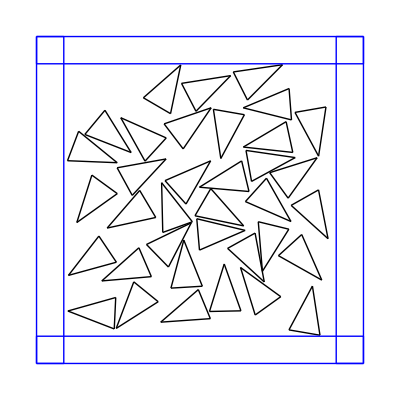

```mathematica
Graphics[{ Black,(Line[#]&/@generateLinesFromPolygon[#])&/@Rest[triList],Blue,(Line[#]&/@generateLinesFromPolygon[#])&/@boundingPoys}]
```

```mathematica
N[Sqrt[3]* Sqrt[2/Sqrt[3]]/2]
```

0.930605

```mathematica
tri1=makeTriangle[10*Random[], 10*Random[], Sqrt[1/Sqrt[3]], Sqrt[3]* Sqrt[1/Sqrt[3]]/2, 2*Pi*Random[]];
triList={};
For[i=1, i<=1000, i++,
newTri=makeTriangle[10*Random[], 10*Random[], Sqrt[4/Sqrt[3]], Sqrt[3]* Sqrt[4/Sqrt[3]]/2, 2*Pi*Random[]];
interSectQ=Complement[Join[polygonIntersectQ[#, newTri]&/@boundingPoys, polygonIntersectQ[#, newTri]&/@triList]];
triList=If[interSectQ=={False}, Append[triList, newTri], triList];
If[Mod[i,100]==0, Print[{i, Length[triList]}]];]
```

{100,21}

{200,26}

{300,29}

{400,32}

{500,34}

{600,34}

{700,36}

{800,36}

{900,36}

{1000,37}

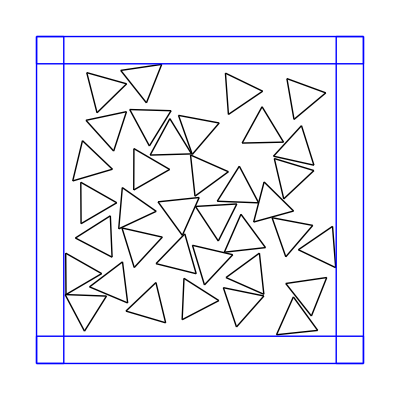

```mathematica
Graphics[{ Black,(Line[#]&/@generateLinesFromPolygon[#])&/@Rest[triList],Blue,(Line[#]&/@generateLinesFromPolygon[#])&/@boundingPoys}]
```

```mathematica
triList={};
For[i=1, i<=1000, i++,
newTri=makeTriangle[10*Random[], 10*Random[], Sqrt[4/Sqrt[3]], Sqrt[3]* Sqrt[4/Sqrt[3]]/2, 2*Pi*Random[]];
interSectQ=Complement[Join[polygonIntersectQ[#, newTri]&/@boundingPoys, polygonIntersectQ[#, newTri]&/@triList]];
triList=If[interSectQ=={False}, Append[triList, newTri], triList];
If[Mod[i,100]==0, Print[{i, Length[triList]}]];]
```

```mathematica
N[Sqrt[1/Sqrt[3]]*Sqrt[3]* Sqrt[1/Sqrt[3]]]
```

1.

```mathematica
makeTriagSet[nn_, L_]:=Module[{triList, newTri, interSectQ},
triList={};
For[i=1, i≤nn, i++,
newTri=makeTriangle[10*Random[], 10*Random[], L, 1/L, 2*Pi*Random[]];
interSectQ=Complement[Join[polygonIntersectQ[#, newTri]&/@boundingPoys, polygonIntersectQ[#, newTri]&/@triList]];
triList=If[interSectQ=={False}, Append[triList, newTri], triList];];
triList];
```

```mathematica
makeTriagSet2[nn_, L_]:=Module[{triList, newTri, interSectQ},
triList={};
For[i=1, i≤nn, i++,
newTri=makeTriangle[10*Random[], 10*Random[], L, 1/L, Pi*Round[3*Random[]]/2];
interSectQ=Complement[Join[polygonIntersectQ[#, newTri]&/@boundingPoys, polygonIntersectQ[#, newTri]&/@triList]];
triList=If[interSectQ=={False}, Append[triList, newTri], triList];];
Print[L];
triList]
```

```mathematica
onePonesey=makeTriagSet[100, 1.1];
```

{100,38}

{200,46}

{300,53}

```mathematica
mo=makeTriagSet2[1000, 0.3+#/10]&/@Range[16];
```

0.4

0.5

0.6

0.7

0.8

0.9

1.

1.1

1.2

1.3

1.4

1.5

1.6

1.7

1.8

1.9

```mathematica
Length[#]&/@mo
```

{61,65,68,69,66,70,73,67,72,68,68,70,61,64,59,59}

```mathematica
Length[mo]
```

16

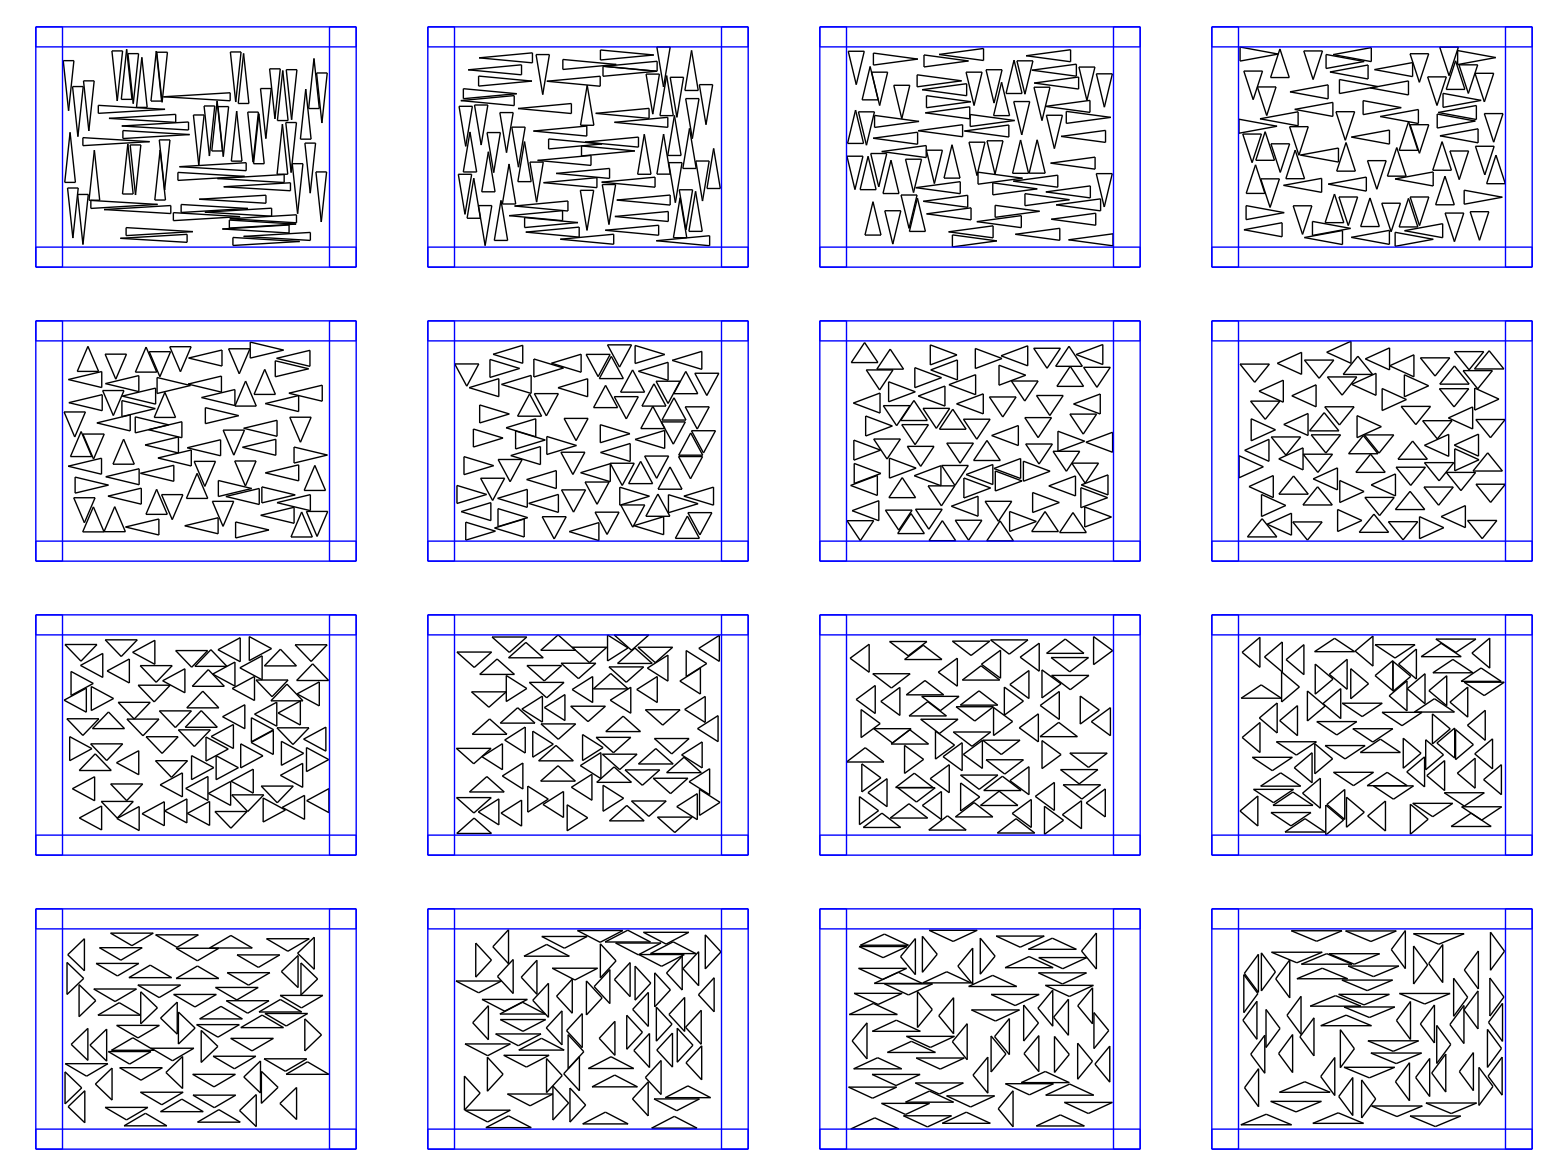

```mathematica
TableForm[Partition[showResults[#]&/@mo,4]]
```

```mathematica
aaa=makeTriagSet[1000, 0.4];
bbb=makeTriagSet[1000, 0.5];
ccc=makeTriagSet[1000, 0.6];
ddd=makeTriagSet[1000, 0.7];
eee=makeTriagSet[1000, 0.8];
fff=makeTriagSet[1000, 0.9];
ggg=makeTriagSet[1000, 1];
hhh=makeTriagSet[1000, 1.1];
iii=makeTriagSet[1000, 1.2];
jjj=makeTriagSet[1000, 1.3];
kkk=makeTriagSet[1000, 1.4];
lll=makeTriagSet[1000, 1.5];
mmm=makeTriagSet[1000, 1.6];
nnn=makeTriagSet[1000, 1.7];
ooo=makeTriagSet[1000, 1.8];
ppp=makeTriagSet[1000, 1.9];
qqq=makeTriagSet[1000, 2];
```

```mathematica
showTriangle[L_]:=Graphics[{ Line[#]&/@generateLinesFromPolygon[makeTriangle[0, 0,L, 1/L, 0]]}]
```

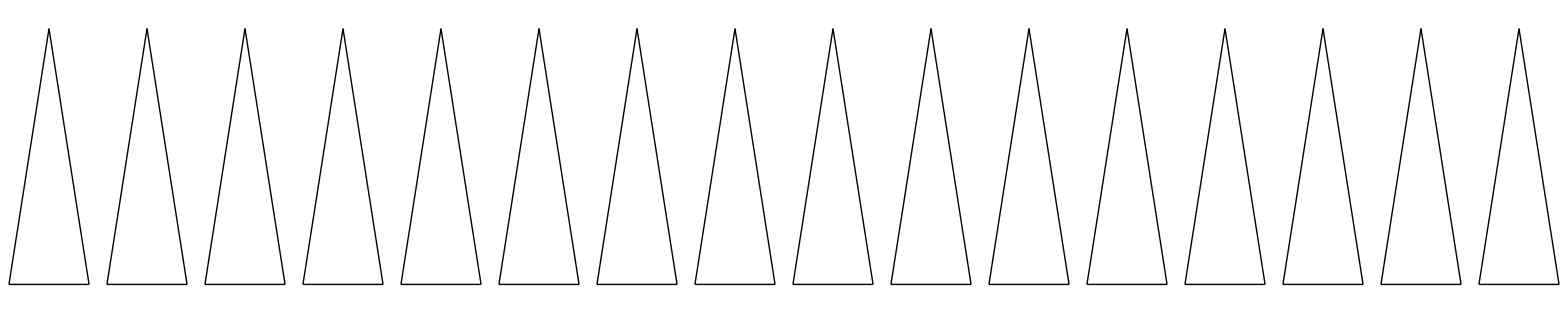

```mathematica
TableForm[{{showTriangle[0.4], showTriangle[0.5], showTriangle[0.6], showTriangle[0.7],showTriangle[0.8], showTriangle[0.9], showTriangle[1], showTriangle[1.1],showTriangle[1.2], showTriangle[1.3], showTriangle[1.4], showTriangle[1.5],showTriangle[1.6], showTriangle[1.7], showTriangle[1.8], showTriangle[1.9]}}]
```

```mathematica
makeTriangle[0, 0,L, 1/L, 0];
```

```mathematica
Length[aaa]
```

43

```mathematica
Length[bbb]
```

52

```mathematica
Length[ccc]
```

51

```mathematica
Length[ddd]
```

62

```mathematica
Length[eee]
```

64

```mathematica
Length[fff]
```

67

```mathematica
Length[ggg]
```

68

```mathematica
Length[hhh]
```

65

```mathematica
Length[iii]
```

69

```mathematica
Length[jjj]
```

64

```mathematica
Length[kkk]
```

63

```mathematica
Length[lll]
```

59

```mathematica
Length[mmm]
```

62

```mathematica
Length[nnn]
```

62

```mathematica
Length[ooo]
```

57

```mathematica
Length[ppp]
```

55

```mathematica
Length[qqq]
```

53

```mathematica
showResults[data_]:=Graphics[{ Black,(Line[#]&/@generateLinesFromPolygon[#])&/@data,Blue,(Line[#]&/@generateLinesFromPolygon[#])&/@boundingPoys}]
```

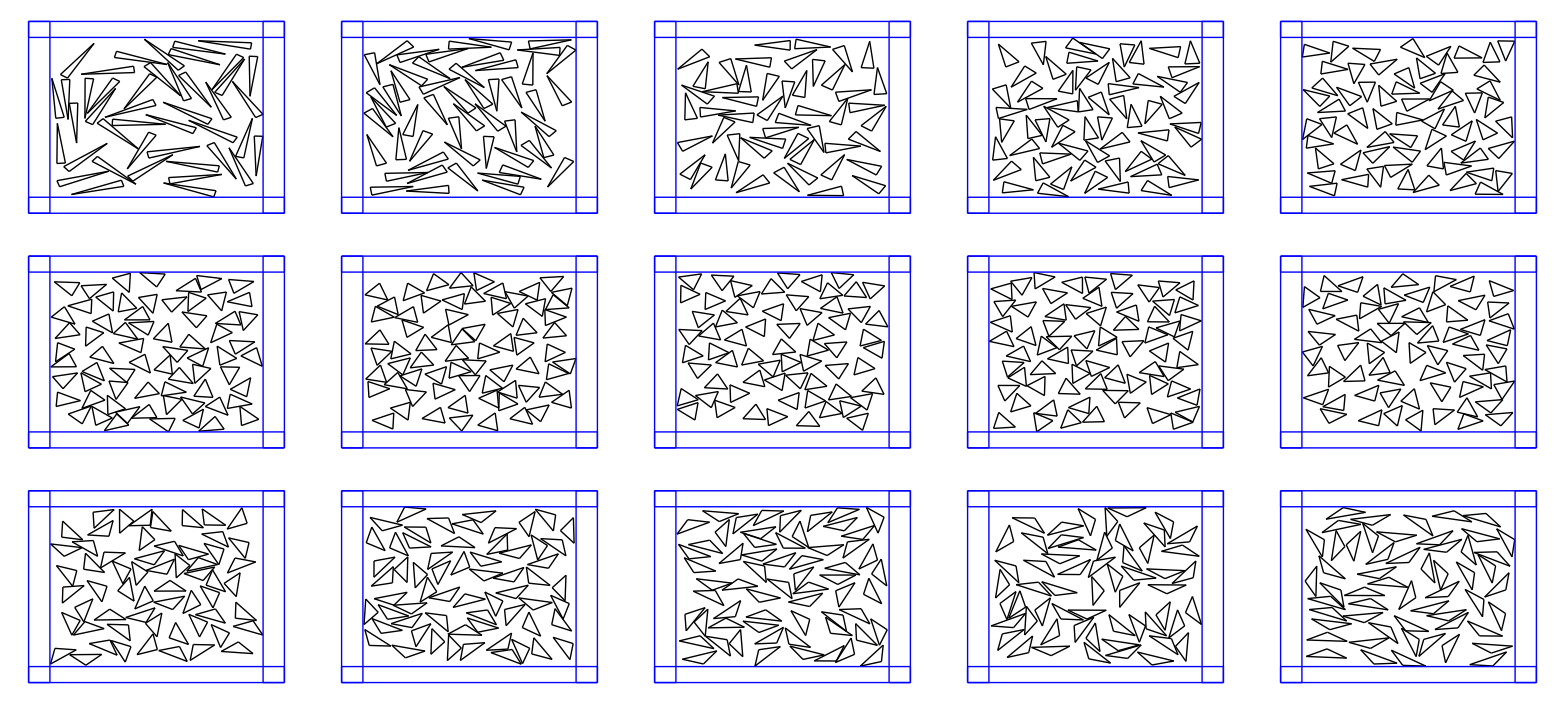

```mathematica
TableForm[{{showResults[aaa], showResults[bbb], showResults[ccc], showResults[ddd], showResults[eee]},
{showResults[fff], showResults[ggg], showResults[hhh], showResults[iii], showResults[jjj ]},
{showResults[lll], showResults[mmm], showResults[nnn], showResults[ooo], showResults[ppp]}}]
```

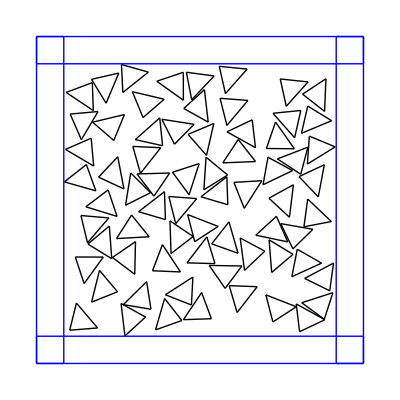

```mathematica
Graphics[{ Black,(Line[#]&/@generateLinesFromPolygon[#])&/@Rest[iii],Blue,(Line[#]&/@generateLinesFromPolygon[#])&/@boundingPoys}]
```